```mathematica
poly=Normal[Series[Cos[x],{x,0,200}]];
```

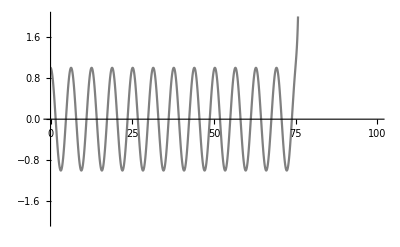

```mathematica
Plot[N[poly/.x->Rationalize[y,10^-3],3],{y,0,100},PlotRange->{-2,2},PlotStyle->{Thick[0.005],Gray}]
```

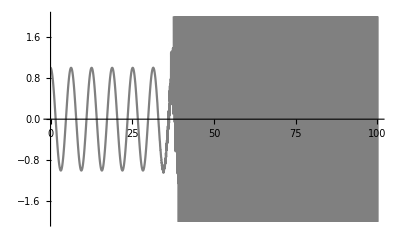

```mathematica
Plot[poly,{x,0,100},PlotRange->{-2,2},PlotStyle->{Thick[0.005],Gray}]
```